```mathematica
ml=.;
mr=.;
d0=.;
d1=.;
d2=.;
t1=.;
t2=.;
tw=.;
Solve[2*ml==(d0+d1)tw-(d0+d1)*2*mr/(d0+d2),d0]
```

{{d0→(2 ml+2 mr-d1 tw-d2 tw+√((2 ml+2 mr-d1 tw-d2 tw)^2+4 tw (2 d2 ml+2 d1 mr-d1 d2 tw)))/(2 tw)},{d0→-(-2 ml-2 mr+d1 tw+d2 tw+√((2 ml+2 mr-d1 tw-d2 tw)^2+4 tw (2 d2 ml+2 d1 mr-d1 d2 tw)))/(2 tw)}}

-1.74204

1.67617

1.82383

2.27107

2.29215

0.9

3.5

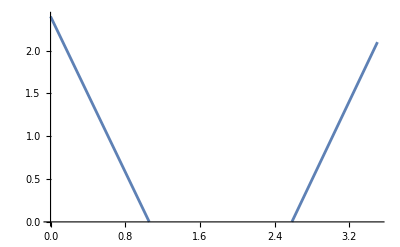

```mathematica
ml=0.6;
mr=0.3;
d1=2.4;
d2=2.1;
tw=3.5;

d0=(2 ml+2 mr-d1 tw-d2 tw+√((2 ml+2 mr-d1 tw-d2 tw)^2+4 tw (2 d2 ml+2 d1 mr-d1 d2 tw)))/(2 tw)
t2=2*mr/(d0+d2)
t1=tw-t2
k1=(d1-d0)/t1
k2=(d2-d0)/t2
f[t_]:=Piecewise[{{d1-t*k1, t<t1},{d0+(t-t1)*k2, t1<=t}}]
Integrate[f[t],{t,0,tw}]
t1+t2
Plot[f[t],{t, 0, tw}, PlotRange->{0,Max[d0, d1, d2]}]
```